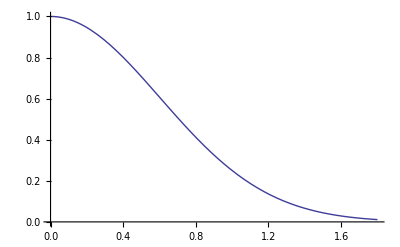

```mathematica
(* "Two methods for antialiased wireframe drawing.. - exponential  *)
dmax = 1.8;
filtExp[x_] :=If[x < dmax, 2^(-2x^2), 0] 
Plot[filtExp[x], {x, 0, dmax}]
```

1.57216-0.708656 x-0.953703 x^2+0.491978 x^3

1.11902

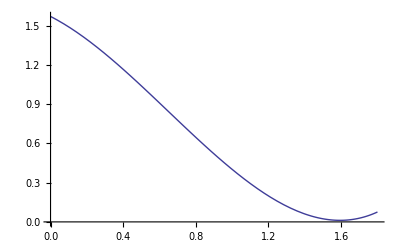

```mathematica
(* RLT *)
transExp[r_] := 2 NIntegrate[filtExp[Norm[{r,x}]], {x, 0, dmax}]
steps = 100.0;
xAtStep[i_] := i dmax / steps
support = Table[0, {i,steps+1}, {j,2}];
For[i=0, i <= steps, i += 1, support[[i+1]] = {xAtStep[i], transExp[xAtStep[i]]}]
interp = Fit[support, {1,x,x^2,x^3}, x]
Integrate[interp, {x, 0, dmax}]
(* ListPlot[supportMN] *)
Plot[interp, {x, 0, dmax}]
```